# Calcium is Complicated: Ca2+ outward, Ca2+ buffering system, Ca2+ inward

## Parameters

```mathematica
(*firstly, ca2+ inward current!*)caInParameters={gca1->0.21,gca2->0.047,kaca1->50,kbca1->16,kaca2->10,vaca1->-11,vbca1->-50,vaca2->22,saca1->-7,sbca1->8,saca2->-7};
```

```mathematica
(*secondly, ca2- outward current! and also some for the concentration state variable*)caOutParameters={g0ca->3.2,ek->-80,koa->600,kob->35,kca->360,vao1->0,vao2->-16,sao1->-23,sao2->-5,f->0.6,c1->2.5,c2->0.7,c3->0.6,ca0->0.05,cica->300};
```

## Steady State Equations and Graphs

```mathematica
(*the Nernst potential of the inward current. When it's calculated, we'll need to evaluate the concentration of Ca2+ at the same time*)eCa[Ca_]:=((8.314*283)/(2*96485.3329))*Log[(13000/Ca)]*1000
```

```mathematica
(*voltage dependencies of the inward current*)aca1VoltDep[V_]:=1/(1+Exp[(V-vaca1)/saca1])/.caInParameters;baca1VoltDep[V_]:=1/(1+Exp[(V-vbca1)/sbca1])/.caInParameters;aca2VoltDep[V_]:=1/(1+Exp[(V-vaca2)/saca2])/.caInParameters;
```

```mathematica
(*voltage dependencies of the outward current*)
a0infinity[V_,Ca_]:=(1/(1+Exp[(V-vao1+f*Ca)/sao1]))*(1/(1+Exp[(V-vao2+f*Ca)/sao2]))*(Ca/(c1+Ca))/.caOutParameters;
b0infinity[Ca_]:=c2/(c3+Ca)/.caOutParameters;
```

```mathematica
{a0Plot100,a0Plot50,a0Plot5,a0PlotHalf,a0PlotTwentieth} =Table[Plot[a0infinity[V,CaVal]/.caOutParameters,{V,-100,100},PlotRange->{{-100,100},{0,1}},GridLines->Automatic],{CaVal,{100,50,5,0.5,0.05}}];
```

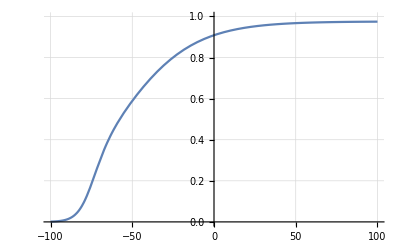

```mathematica
(*compared to the paper's results, this graph has a longer lag at the beginning and a much shallower slope.*)Show[a0Plot100]
```

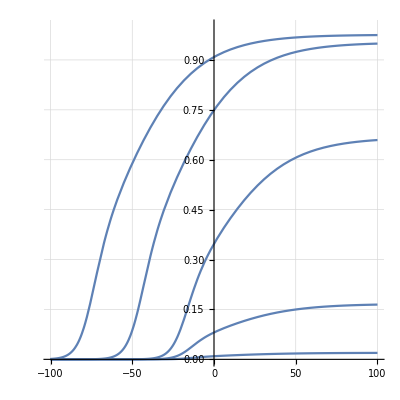

```mathematica
Show[a0Plot100,a0Plot50,a0Plot5,a0PlotHalf,a0PlotTwentieth,AspectRatio->1]
```

## Initial Activations and In activations

### Inward

```mathematica
(*initial activation 1*)initialActivation1=NDSolve[{aca1'[t]==(aca1VoltDep[-40]-aca1[t])*kaca1,aca1[0]==0}/.caInParameters,aca1[t],{t,0,100000}];
```

```mathematica
aca1[t]/.initialActivation1[[1,All]]/.t->100000
```

0.0156293

```mathematica
(*initial inactivation 1*)
initialInactivation1=NDSolve[{baca1'[t]==(baca1VoltDep[-40]-baca1[t])*kbca1,baca1[0]==0}/.caInParameters,baca1[t],{t,0,100000}];
```

```mathematica
baca1[t]/.initialInactivation1[[1,All]]/.t->100000
```

0.2227

```mathematica
(*initial activation 2*)
initialActivation2=NDSolve[{aca2'[t]==(aca2VoltDep[-40]-aca2[t])*kaca2,aca2[0]==0}/.caInParameters,aca2[t],{t,0,100000}];
```

```mathematica
aca2[t]/.initialActivation2[[1,All]]/.t->100000
```

0.000142341

### Outward

I wonder if this is the problem area: can we use ca0 when we find steady state activation/inactivation? Or do I need to evaluate this with the Calcium differential equation? This does get calculated after the inward current, so it would be possible.

```mathematica
(*initial activation*)initialActivation1Outward=NDSolve[{a0'[t]==(a0infinity[-40,ca0]-a0[t])*koa,a0[0]==0}/.caOutParameters,a0[t],{t,0,100000}];
```

```mathematica
a0[t]/.initialActivation1Outward[[1,All]]/.t->100000
```

0.0000240847

```mathematica
(*initial inactivation*)
initialInactivation1Outward=NDSolve[{b0'[t]==(b0infinity[ca0]-b0[t])*kob,b0[0]==0}/.caOutParameters,b0[t],{t,0,100000}];
```

```mathematica
b0[t]/.initialInactivation1Outward[[1,All]]/.t->100000
```

1.07692

```mathematica
(*let's try evaluating initial in/activations with the Ca concentration allowed to vary, assuming the voltage clamp affects calcium levels*)initialActivationOutwardTry2=NDSolve[{a0'[t]==(a0infinity[-40,Ca[t]]-a0[t])*koa,a0[0]==0,Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(-40(*put in for v[t]*)-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,aca1'[t]==(aca1VoltDep[-40]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[-40]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[-40]-aca2[t])*kaca2,Ca[0]==ca0,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884}/.caInParameters/.caOutParameters,{a0[t],Ca[t],aca1[t],baca1[t],aca2[t]},{t,0,100000}];
```

```mathematica
a0[t]/.initialActivationOutwardTry2[[1,All]]/.t->100000
```

0.0000747464

```mathematica
initialInactivationOutwardTry2=NDSolve[{b0'[t]==(b0infinity[Ca[t]]-b0[t])*kob,b0[0]==0,Ca'[t]==-cica*((gca1*aca1[t]*baca1[t]+gca2*aca2[t])*(-40(*put in for v[t]*)-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,aca1'[t]==(aca1VoltDep[-40]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[-40]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[-40]-aca2[t])*kaca2,Ca[0]==ca0,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884}/.caInParameters/.caOutParameters,{b0[t],Ca[t],aca1[t],baca1[t],aca2[t]},{t,0,100000}];
```

```mathematica
b0[t]/.initialInactivationOutwardTry2[[1,All]]/.t->100000
```

0.921843

## Buffering System

```mathematica
(*first try at getting the buffering system to work. This is being held at one voltage, so I wouldn't expect any values to change. When we start analyzing calcium currents over voltages or over time*) caBuffer=NDSolve[{Ca'[t]==-cica*((gca1*aca1[t]*baca1[t]+gca2*aca2[t])*(-40(*put in for v[t]*)-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,aca1'[t]==(aca1VoltDep[-40]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[-40]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[-40]-aca2[t])*kaca2,Ca[0]==ca0,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884}/.caInParameters/.caOutParameters,{Ca[t],aca1[t],aca2[t],baca1[t]},{t,0,100000}];
```

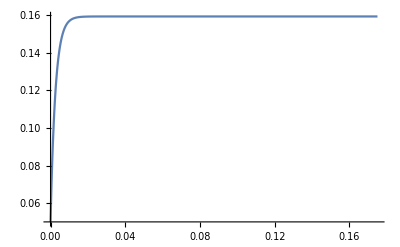

```mathematica
Plot[Ca[t]/.caBuffer[[1,All]],{t,0,0.175},PlotRange->Full]
```

```mathematica
Ca[t]/.caBuffer[[1,All]]/.t->100000
```

0.159349

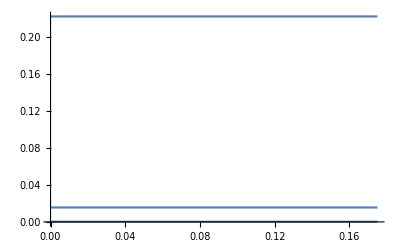

```mathematica
Plot[{aca1[t],aca2[t],baca1[t]}/.caBuffer[[1,All]],{t,0,0.175}]
```

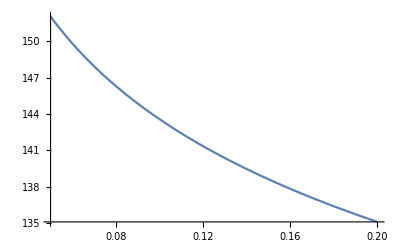

```mathematica
(*maybe I should use the apparent steady state calcium concentration in the system below? I want to see what each of the parts does, let's graph eCa*)Plot[eCa[ca],{ca,ca0,0.2}/.caOutParameters]
```

## Replicate Ca2+ Outward Graphs

```mathematica
(*first, set up the differential equations - including the calcium buffer system.*)
{caOutNeg30,caOutNeg20,caOutNeg10,caOut0,caOut10,caOut20}=Table[NDSolve[{Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,aca1'[t]==(aca1VoltDep[V[t]]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[V[t]]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[V[t]]-aca2[t])*kaca2,Ca[0]==0.15934876118185337+ca0(*trying this value. no effect*),
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884,(*and now the outward calcium eqs. Should this include the inward current as well, to account for it's effect on voltage?*)1700*V'[t]==-((g0ca*a0[t]*b0[t]*(V[t]-ek))+(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))),a0'[t]==(a0infinity[V[t],Ca[t]]-a0[t])*koa,a0[0]==0.00007448265106619814,b0'[t]==(b0infinity[Ca[t]]-b0[t])*kob,b0[0]==0.9218425521765746,V[0]==initV}/.caInParameters/.caOutParameters,{Ca[t],aca1[t],aca2[t],baca1[t],V[t],a0[t],b0[t]},{t,0,100000}],{initV,{-30,-20,-10,0,10,20}}];
```

Adding the inward current to the voltage calculation had no qualitative effect.

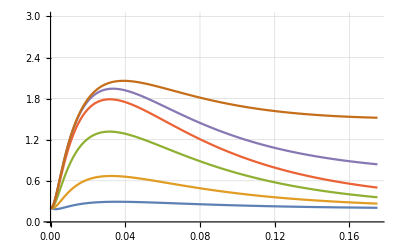

```mathematica
Plot[{Ca[t]/.caOutNeg30[[1,All]],Ca[t]/.caOutNeg20[[1,All]],Ca[t]/.caOutNeg10[[1,All]],Ca[t]/.caOut0[[1,All]],Ca[t]/.caOut10[[1,All]],Ca[t]/.caOut20[[1,All]]},{t,0,0.175},PlotRange->{{0,.175},{0,3}},GridLines->Automatic]
```

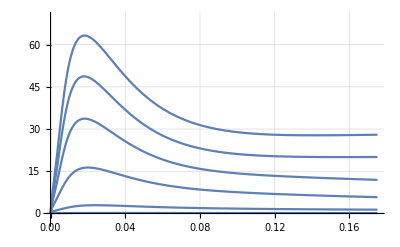

```mathematica
(*outward current plot*)Plot[{g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg30[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg20[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg10[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut0[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut10[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut20[[1,All]]}/.caOutParameters/.caInParameters,{t,0,.175},PlotRange->{{0,.175},{-3,70}},GridLines->Automatic]
```

## Normalized Conductance, Outward

```mathematica
(*fig2C*)

{normCond30,normCond20,normCond10,normCond0,normCondNeg10}=Table[Plot[a0infinity[V,Ca]*b0infinity[Ca]/.caOutParameters,{Ca,0,20},PlotRange->{{0,20},{0,0.12}}],{V,{30,20,10,0,-10}}];
```

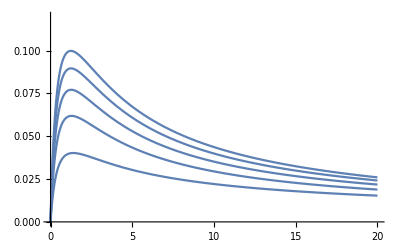

```mathematica
Show[normCond30,normCond20,normCond10,normCond0,normCondNeg10](*behavior is accurate for the most positive voltages, but totally off for the negative/0 voltages*)
```